# Model-based simulation of the Io Plasma Torus

## From a simple density model to the radiometric observables and their visualization

Giuliano Vinci

PhD student in Aerospace Sciences and Technologies (DAST@DIN). Email: giuliano.vinci@unibo.it.

## Introduction

In this Wolfram notebook, the objective is to define the key parameters and functions needed to build the model described in Phipps et al., 2017 ([1], see the references at the end of this introductory section). This empirical model predicts the number density of electrons in the region around Jupiter. Such models are currently used in the domain of radio sciences to calibrate the plasma-related noise affecting the propagation of radio signals in space ([2]). The contents are developed as follows:

- In the first section, physical constants and models are defined. Specifically, the plasma model is defined as a couple of piecewise-defined GMMs (where GMM stands for Gaussian Mixture Model), each of which is activated in a specific region through a conditional check. 
	- In 1.1, the physical constants are introduced. 
	- In 1.2, the model functions are implemented. 
	- In 1.3, the Line of Sight (LOS) integral is defined as a function to compute the TEC (Total Electron Content, meant along a LOS).
	- In 1.4, some tests are provided to the user/developer to check the soundness of the definitions.
	
- In the second section, the TEC-computing routine is leveraged to evaluate the Path Delay and the Doppler Shift over a certain, made-up, circular trajectory of the Juno spacecraft (whose real trajectory, however, is sufficiently close to the one here proposed, see [3]). 
	- In 2.1, some orbital parameters for the probe and Jupiter are provided.
	- In 2.2, the trajectory of the spacecraft is generated.
	- In 2.3, the viewing geometry of Earth is defined. To simplify the problem, it is assumed that the Earth and Jupiter orbit on the same plane, and that the centrifugal equator of Jupiter, which is the equator of the observer, is at about 7-8 degrees with respect to the Jovigraphic equator, assumed co-planar with the orbit of Earth. This entails some approximation, as does the assumption that the viewing geometry of Earth is constant during a passage of the probe (which is not entirely true, since Jupiter spins at 1 rotation every 10 hours).
	- In 2.4, the computation of Path Delays (PD) and Doppler Shifts (DS) takes place, if DoneAlready is “False”. Since the computation can take some time, the notebook is provided with a precomputed table of PDs and DSs, equal to the one which would be generated if DoneAlready = False. When DoneAlready = True, the code imports the data tables and proceeds further.

- In the third section, some plots are shown to prove the similarity with the plots of the original paper. Some discrepancy may remain, but the overall shape of the curves matches well. 
	- In 3.1, a radial density profile on the centrifugal equator (equatorial plane of the reference system taken into account) is depicted. 
	- In 3.2, a 2D color map of the density of electrons around Jupiter is shown. This 2D map also includes the trajectory of the Juno spacecraft (simulated with some simplifications, i.e. circular polar orbit at 3 RJ) and a diagram representing the radio link from the spacecraft to the Earth. Specifically:
		- In 3.2.1, the quantities are initialized.
		- In 3.2.2, the plot is created.
	- In 3.3, a series of grid plots, representing the simulated Path delays and Doppler shifts, are shown. A deeper description of these radiometric observables will be given below.

Notice: The suppressed warnings were mostly related to numerical precision issues, hence the decision to ignore them.

### Formulas

Some reference formulas for Total Electron Content, Path Delay and Doppler Shift (taken from [2]):

Total Electron Content (TEC) along a line of sight from , the spacecraft position, to , the ground station equipped with receiving antennas. Formula: 	.

Phase Path Delay encountered by a carrier wave when crossing a dispersive (i.e. frequency-dependent) medium. TEC is the total electron content, and . In the code, corrections for measurement units (from cubic centimeters to cubic meters, and from meters to millimeters) are applied. Lastly, the result is multiplied by , so to have it in length units. Formula:
 .

Doppler Shift (in units of )encountered by a carrier when traversing a dispersive medium. k_d is a dimensional constant. The value is finally multiplied by 100 to give a percentage. Formula:

### References

1. Phipps, P. H. & Withers, P. Radio occultations of the Io plasma torus by Juno are feasible. Journal of Geophysical Research: Space Physics 122, 1731–1750 (2017). DOI: 10.1002/2016JA023447.
2. Asmar, Sami W. Planetary Atmospheres, Rings, and Surfaces. in Radio Science Techniques for Deep Space Exploration, pages 39–68 (John Wiley & Sons, Ltd, 2022). DOI:10.1002/9781119734178.ch2.
3. Bolton, S. et al. The Juno Mission. Space Science Reviews 213, 5–37 (2017). DOI: 10.1007/s11214-017-0429-6.

## 1) Definition and testing of models and constants

### 1.1 Defining all the physical constants

: Jupiter Radius
: Earth Radius
: Semi-major axis of Jupiter
: Semi-major axis of Earth
: Transponding ratio in X/X band for the spacecraft
: Base unaltered carrier frequency

```mathematica
(*Constants in Jupiter radii (RJ)*)
RJ=71492*10^3; (*Jupiter radius in meters*)
REa = 6378000; (*Earth radius in meters*)
rIo=5.9 RJ;      (*Io's orbital distance in meters*)
rThreshold = 6.1 RJ; (*Distance threshold for model switch*)
AU = 149597871 * 10^3; (*Value of 1 Astronomical Unit in meters*)
cent3metr3 = 100*10^3; (*The number of cubic centimeters in a cubic meter, used to convert densities from cm^-3 to m^-3*)
m2mm = 1000; (*Millimeters in a meter*)

JupiterSma = 5.2033 * AU;  (*Semimajor axis of Jupiter in Jovian Radii*)
EarthSma = 1 AU; (*Semimajor axis of Earth in Jovian Radii*)

c0 = 299792458; (*Speed of Light in meters/seconds*)
ε0=8.8541878128*10^(−12) ; (*Dieletric constant of vacuum in units of [C2N−1m−2]*) 
qE = 1.602176634*10^(−19); (*Elementary charge in [C]*)
mE = 9.1093837139*10^(−31); (*Mass of the electron [Kg]*)

kEl = qE^2/(8*Pi^2*mE*ε0); (*Constant to convert TEC to Doppler phase delay*)

(*Definition of the symbolic and numerical parameters for the torus models *)
parameters={N01,N02,N03,H1,H2,H3,R1,R2,R3,W1,W2,W3,N04,H4,R4,W4};
paramsRules={N01->1710,H1->0.1 RJ,R1->5.23 RJ,W1->0.2 RJ,N02->2180,H2->0.6 RJ,R2->5.6 RJ,W2->0.08 RJ,N03->2160,H3->1.0 RJ,R3->5.89 RJ,W3->0.32 RJ, N04 -> 1601, H4 -> 1.0 RJ, R4 -> 5.53 RJ, W4 -> 1.88 RJ};
numericalP = parameters/.paramsRules;

(*Frequency properties*)
fCarrier = 7.2 * 10^9; (*Definition of the S/C carrier frequency [Hz]*)
M2=1.1748998664886516;  (*Transponding ratio for X/X TX/RX*)
F2 = 1/M2^2; (*F2 ratio*)

(*Transformations of coordinates: from Spherical to Cartesian*)
Sph2CarP[posRTP_]:= Module[{x, y, z}, 
x = posRTP[[1]]*Cos[posRTP[[2]]]*Cos[posRTP[[3]]];
y = posRTP[[1]]*Cos[posRTP[[2]]]*Sin[posRTP[[3]]];
z = posRTP[[1]]*Sin[posRTP[[2]]];
{x, y, z}
];

(*Transformations of coordinates: from Cartesian to Spherical*)
Car2SphP[posXYZ_]:= Module[{r, theta, phi}, 
r = Sqrt[posXYZ[[1]]^2 + posXYZ[[2]]^2+ posXYZ[[3]]^2];
theta = ArcSin[posXYZ[[3]]/r];
phi = ArcTan[posXYZ[[2]]/posXYZ[[1]]];
{r, theta, phi}
];
```

### 1.2 Definition of density models

```mathematica
(*Definition of density model for the inner torus*)
InnerDensModel[X_,P_]:=Module[{N01,N02,N03,H1,H2,H3,R1,R2,R3,W1,W2,W3,R,Theta,Phi,rho,z,dRho1,dRho2,dRho3},(*Estrazione dei parametri da P*)
{N01,N02,N03,H1,H2,H3,R1,R2,R3,W1,W2,W3}=P;
(*Estrazione delle coordinate da X*)
{R,Theta,Phi}=X;
(*Cylindrical distance*)
rho=R*Cos[Theta];
(*Height above the centrifugal equator*)
z=R*Sin[Theta];

dRho1=rho-R1;
dRho2=rho-R2;
dRho3=rho-R3;

(*Cold torus+Ribbon torus+Warm torus*)
N01 Exp[-(dRho1^2/W1^2)] Exp[-(z^2/H1^2)]+N02 Exp[-(dRho2^2/W2^2)] Exp[-(z^2/H2^2)]+N03 Exp[-(dRho3^2/W3^2)] Exp[-(z^2/H3^2)]
];
 
OuterDensModel[X_,P_]:=Module[{N04,H4,R4,W4,R,Theta,Phi,rho,z,dRho4},(*Parameters extracted from P*){N04,H4,R4,W4}=P;
(*Coordinates extracted from X*)
{R,Theta,Phi}=X;
(*Cylindrical distance*)
rho=R*Cos[Theta];
(*Height above the centrifugal equator*)
z=R*Sin[Theta];

dRho4=rho-R4;
(*Outer Torus*)
N04 Exp[-(dRho4^2/W4^2)] Exp[-(z^2/H4^2)]
];


Density[X_,P_]:=With[{P1=P[[1;;12]],P2=P[[13;;All]],rThreshold=6.1 RJ},Module[{rho},rho=X[[1]] Cos[X[[2]]];
If[rho<rThreshold,InnerDensModel[X,P1],OuterDensModel[X,P2]
] (*If closure*)
] (*Module closure*)
] (*With closure*)
```

### 1.3 Definition of the Line of Sight Integral and Group Path Delay

```mathematica
(*Function to compute the Line Of Sight Integral (LOS)*)
LineOfSightIntegral[scPosRTP_,earthPosRTP_,P_]:=Module[{rFunc,t, dist, Threshold, distFromJupiter, tMax, scPosXYZ, earthPosXYZ, numericalP, integrand},

scPosXYZ = Sph2CarP[scPosRTP];
earthPosXYZ = Sph2CarP[earthPosRTP];

(*Parametrize the straight line between the Spacecraft and Earth*)
rFunc[t_]:=scPosXYZ+t (earthPosXYZ-scPosXYZ);

(*Compute distance between Earth and Spacecraft*)
dist=Norm[earthPosXYZ-scPosXYZ];

(*Function to compute the distance from Jupiter at any point r(t)*)
distFromJupiter[t_]:=Norm[rFunc[t]];

(*Set maximum integration distance to 15 RJ*)
Threshold = 20 ;

(*Find the value of t where the distance from Jupiter reaches 15 RJ*)
tMax=Quiet@Check[FindRoot[distFromJupiter[s]/RJ==20,{s,0,1}],1 ];

(*Definition of the integrand function*)
integrand[s_]:=Check[Density[Car2SphP[rFunc[s]], P], 0]; 

      (*Limit t to between 0 and tMax (or 1 if the distance limit is never reached)*)
	dist * cent3metr3 * NIntegrate[integrand[s],{s,0,Min[s/.tMax,1]}, WorkingPrecision->50, Method->{"AdaptiveMonteCarlo", "MaxPoints"->100000}]
];

(*This function computes the path delay in millimeters*)
GroupPathDelay[ScPos_, EarthPos_, fCarrier_] := Module[{TEC},
TEC = LineOfSightIntegral[ScPos, EarthPos,numericalP];
-m2mm*(kEl/fCarrier^2)*TEC
];
```

### 1.4 Tests

```mathematica
Density[{20 RJ, 0 Degree, 0 Degree}, numericalP]
```

2.99511×10^-23

```mathematica
scPos = {3 RJ, 0 Degree, 0 Degree};
EaPos = {JupiterSma - EarthSma, 0Degree, 0 Degree};

Quiet[GroupPathDelay[scPos, EaPos, fCarrier]]
```

-20.9095

```mathematica
scPosXYZ = Sph2CarP[scPos];
earthPosXYZ = Sph2CarP[EaPos];

(*Parametrize the straight line between the Spacecraft and Earth*)
rFunc[t_]:=scPosXYZ+t (earthPosXYZ-scPosXYZ);
distFromJupiter[t_]:=Norm[rFunc[t]];
distFromJupiter[0+0.002]/RJ
FindRoot[distFromJupiter[s]/RJ==Threshold,{s,0,1}];
```

## 2) Creation of an orbit for the spacecraft to simulate the radiometric observables (Path delay and Doppler shift)

### 2.1 Definition of orbital parameters for the Spacecraft, Earth and Jupiter

```mathematica
(*Orbital Parameters*)
muJupiter = 126.687*(10^6)*(10^9); (*Jupiter's gravitational parameter in m^3/s^2*)

inclination=90 Degree;  (*Example inclination,adjust as needed*)

semiMajorAxis=3*RJ;  (*Example orbit at 3 Jupiter radii*)

meanMotion = Sqrt[muJupiter/semiMajorAxis^3]; (*Mean motion of the S/C around Jupiter*)

numPoints=100;  (*Number of sampled points along the orbit*)

initTime = 0 ;  (*Initial time tag*)
```

### 2.2 Creation of the list of spacecraft positions

```mathematica
(*Generate latitudes from North Pole (π/2) to South Pole (-π/2)*)
latitudes=Subdivide[-Pi/2,+Pi/2,numPoints-1];  (*Uniform sampling*)

(*Computation of the time tags (in seconds past beginning) of the Spacecraft positions*)
times = Table[initTime + (latitudes[[i]] - latitudes[[1]])/meanMotion, {i, 1, numPoints}];

(*Conversion of times to hours*)
timesHrs = times/3600;

(*Generate longitudes*)
longitudes = Table[0.0, {numPoints}];

(*Generate spacecraft positions:{Distance from Jupiter,Latitude}*)
scPositions=Table[{semiMajorAxis,lat, longitudes[[1]]},{lat,latitudes}];

(*Generate cylindrical coordinates for S/C positions*)
scPositionsCyl=Table[{semiMajorAxis*Cos[lat],semiMajorAxis*Sin[lat]},{lat,latitudes}];
```

### 2.3 Definition of Earth angles

```mathematica
(*Apparent Earth angle semi-range*)
earthSemiAngle = 8 Degree;

(*Create a Table of Earth viewing angles*)
EarthAngles=Table[angle,{angle,-earthSemiAngle,earthSemiAngle,1 Degree}];

(*Earth Positions in Spherical Coordinates referred to Jupiter centrifugal equator*)
EarthPos=Table[{JupiterSma - EarthSma, angle, 0 Degree},{angle, EarthAngles}];
```

### 2.4 Computation of group Path Delay and Doppler Shift

```mathematica
DoneAlready = True;

(*Simplified Doppler constant: ((F2*M2*fCarrier/c0)/(c0*fCarrier/100)) -> 100/M2*c0^2 -> 100/M2*)
DopplerDimConst = 100/M2;

PDtablefile = FileNameJoin[{NotebookDirectory[], "PD_table.csv"}];
DStablefile = FileNameJoin[{NotebookDirectory[], "DS_table.csv"}];

If[DoneAlready==True,
( GroupPdTable=Import[PDtablefile, "CSV"];
DopplerSTable = Import[DStablefile, "CSV"];
),
(GroupPdTable= Quiet[Table[
Module[{scPos = scPositions[[i]], EaPos=EarthPos[[j]]},
GroupPathDelay[scPos, EaPos, fCarrier]
],
{i, 1, numPoints}, {j, 1, Length[EarthPos]}]];


DopplerSTable=Quiet[DopplerDimConst*Table[Differences[GroupPdTable[[All,j]]]/Differences[times],{j,1,Length[EarthPos]}]];
Export[PDtablefile, GroupPdTable, "CSV"];
Export[DStablefile, DopplerSTable, "CSV"];
)
 ]
```

```mathematica
(*Print[GroupPdTable]*)
```

## 3) Plots of the outputs

### 3.1 Plot of Density along the equator

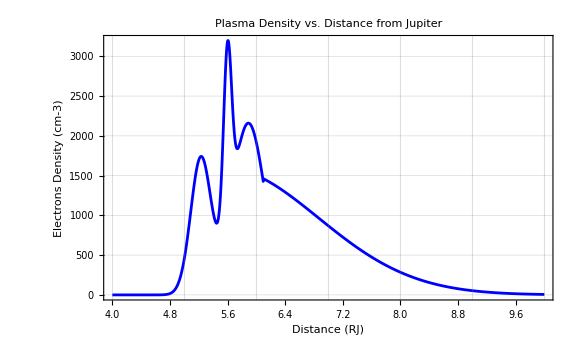

```mathematica
Plotname1D = FileNameJoin[NotebookDirectory[], "Radial_density_profile.png"];

testDistance = Subdivide[4 RJ, 10 RJ, 1000-1];
testPos=Table[{r,0 Degree, 0 Degree},{r,testDistance}];
testDensity = Table[Density[pos, parameters/.paramsRules], {pos, testPos}];

(*Plotting Density vs.Distance*)
ListLinePlot[
Transpose[{testDistance/RJ,testDensity}],(*Plotting distance in RJ*)AxesLabel->{"Distance from Jupiter (RJ)","Plasma Density"},PlotLabel->"Plasma Density vs. Distance from Jupiter",PlotStyle->Blue,PlotRange->{{4,10},Automatic},(*Force x-axis from 4 RJ to 10 RJ*)
Frame->True,(*Adds a frame around the plot*)FrameLabel->{"Distance (RJ)","Electrons Density (cm-3)"},
ImageSize -> Large,
GridLines->{Range[4,10,1],Automatic}  (*Add grid lines at each RJ*)]
```

```mathematica
Export[Plotname1D, %];
```

### 3.2 Color plot of the Density around Jupiter

#### 3.2.1 Constants and other initializations for the plot

```mathematica
(*Define the range of radial distances from 4 RJ to 10 RJ*)
radialDistances=Subdivide[4 RJ,10 RJ,100];  (*101 points*)

(*Define the range of latitudes from-Pi/2 (South Pole) to Pi/2 (North Pole)*)
latitudes=Subdivide[-Pi/2,Pi/2,100];  (*101 points*)

(*Create a grid of points in spherical coordinates:{R,Theta,Phi}*)
gridPoints=Flatten[Table[{r,theta,0 Degree},{r,radialDistances},{theta,latitudes}],1];

(*Create a grid of points to represent cylindrical coordinates*)
gridPointsRZ = N[Flatten[Table[{r*Cos[theta], r*Sin[theta]}, {r, radialDistances}, {theta, latitudes}], 1]];

(*Compute density for each point in the spherical grid*)
densityGrid=Quiet@Flatten[Table[Density[{r,theta,0 Degree},parameters/. paramsRules],{r,radialDistances},{theta,latitudes}]];

(*Combine everything into a single, filtered dataset*)
densityData=Transpose[{gridPointsRZ[[All,1]],gridPointsRZ[[All,2]],densityGrid}];
filteredDensityData=Select[densityData,-4 RJ<=#[[2]]<=4 RJ&]; (*Remove the points which are too high above the centrifugal equator*)

(*Definition of colors and file names*)
zeroColor=ColorData["SunsetColors"][0]; (*Background color equal to the one used for zero-value points in the plot*)
jupiterColor=RGBColor[0.89,0.63,0.17]; 
earthColor=RGBColor[0.0,0.5,1.0];
JupiterCartoonFile = FileNameJoin[{NotebookDirectory[], "Jupiter_cartoon.png"}];
JunoCartoonFile = FileNameJoin[{NotebookDirectory[], "Juno_cartoon.png"}];
EarthCartoonFile = FileNameJoin[{NotebookDirectory[], "Earth_cartoon.png"}];
Plotname2D = FileNameJoin[NotebookDirectory[], "Electrons_2D_plot.png"];

(*Defining a sample position of Juno to plot*)
junoPosRTP={3 RJ,20 Degree, 0 Degree};
junoPosXYZ = Sph2CarP[junoPosRTP];
junoPos = {junoPosXYZ[[1]], junoPosXYZ[[3]]};

(*Defining a sample Earth position as seen from Jupiter*)
earthPosXYZ = Sph2CarP[{JupiterSma - EarthSma, -10 Degree, 0 Degree}];
earthPosVersor = (earthPosXYZ - junoPosXYZ)/Norm[(earthPosXYZ - junoPosXYZ)]; (*Normalized direction of Earth*)

(*Creation of a point which stands in the line between the S/C and Earth, at about 10 RJ from Jupiter -> Proximal Earth Point*)
earthPosProxXYZ[d_?NumericQ]:=Norm[N[junoPosXYZ/RJ+d*earthPosVersor]];
earthPos10RJ = junoPosXYZ + 7.0*earthPosVersor*RJ;
earthPoint = N[{earthPos10RJ[[1]], earthPos10RJ[[3]]}];
```

#### 3.2.2 Execution of the 2D density plot

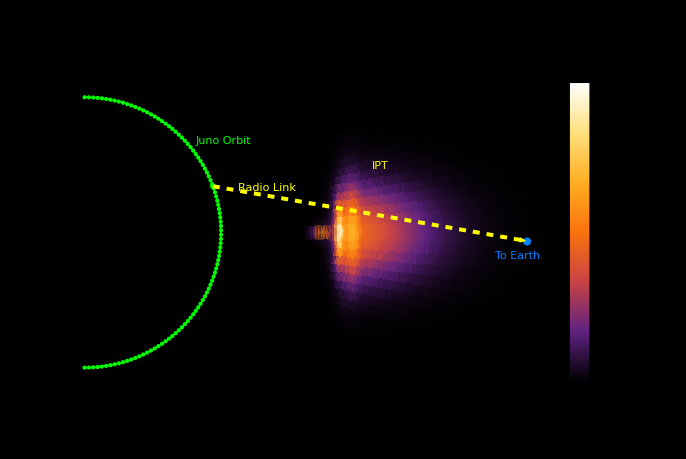

```mathematica
(*Execution of the plot*)
ListDensityPlot[filteredDensityData,
ColorFunction->"SunsetColors",
Frame->{Placed["Radial Cylindrical Distance: X (RJ)", Below],
Placed["Height over centrifugal equator: Z (RJ)", Left]},
PlotLabel->Style["Plasma Density Around Jupiter",Bold,14, White],
PlotLegends->BarLegend[Automatic,
LabelStyle->{Black,Bold,14},
LegendLabel->Style["Electrons Density (cm⁻.b3)",Black,Bold,16],
LegendMarkerSize->{30,500}
],
Epilog->{
(*Draw Jupiter as a cartoon*)
Inset[Import[JupiterCartoonFile],{0,0},Center,Scaled[0.25]],
Style[Text["Jupiter",{1.05 RJ, 1.05 RJ}],jupiterColor,Italic,14],

(*Orbit of Juno*)
Green,Line[scPositionsCyl],PointSize[Small],Point[scPositionsCyl], Style[Text["Juno Orbit",{3.05 RJ,2.05 RJ}],Green,Bold,12],

(*Position of Juno (cartoon of the S/C)*)
Inset[Import[JunoCartoonFile],junoPos,Center,Scaled[0.1]],

(*Position of the Proximal Earth Point, drawn as a small Earth*)
earthColor,Disk[earthPoint,REa],
Inset[Import[EarthCartoonFile], earthPoint, Center, Scaled[0.024]],
Style[Text["To Earth",earthPoint+{-0.2 RJ,-0.3 RJ}],earthColor,Italic,14],

(*Draw a dashed arrow line towards the Proximal Earth Point*)
Yellow,Dashed,Thickness[0.005],Arrowheads[0.03],Arrow[{junoPos,earthPoint}],
Style[Text["Radio Link",{4. RJ, 1 RJ}],Yellow,Italic,12],

(*Add a label for the IPT*)
Style[Text["IPT",{6.5 RJ, 1.5 RJ}],Pink,Bold,14]
},
ImageSize->Large,
Frame->False,
Axes->True,
AxesStyle->Directive[White,Thick],
PlotRange->All,
PlotRangePadding->None,
AspectRatio->Automatic,(*Ensure equal scaling for both axes*)
Background->zeroColor,
InterpolationOrder->3,
Ticks->{Table[{i,i/RJ},{i,Min[densityData[[All,1]]],Max[densityData[[All,1]]],RJ}],Table[{i,i/RJ},{i,-4 RJ,4 RJ,RJ}]}]
```

```mathematica
Export[Plotname2D,%];
```

### 3.3 Table of plots of Path Delay and Doppler Shift

```mathematica
(*Define time units for the x-axis label*)
timeLabel="Time (hours past T0)";
timeRange = {Min[timesHrs],Max[timesHrs]};

(*Generate plots for each Earth viewing angle*)
tabs=AssociationThread[Row[{Subscript["θ","Ea"]," = ",ToString[Round[#/Degree]],"°"}]&/@EarthAngles,Table[
Grid[{
{ListLinePlot[
Transpose[{timesHrs,GroupPdTable[[All,j]]}], (*Plot of the Path Delay as a function of time*)
PlotStyle->{Thick,Blue},
AxesLabel->{timeLabel,"Path Delay (mm)"},
PlotLabel->Style[Row[{"Group Path Delay (",Subscript["θ","Ea"]," = ",ToString[Round[EarthAngles[[j]]/Degree]],"°)"}],Bold,16],
ImageSize->Large,
GridLines->Automatic,
PlotRange->{timeRange, {-25, 5}}
]},
{ListLinePlot[
Transpose[{Most[timesHrs],DopplerSTable[[j]]}], (*Plot of the Doppler Shift as a function of time*)
PlotStyle->{Thick,Red},
AxesLabel->{timeLabel,"Doppler (100*Δf/f0)"},
PlotLabel->Style[Row[{"Doppler Shift (",Subscript["θ","Ea"]," = ",ToString[Round[EarthAngles[[j]]/Degree]],"°)"}],Bold,16],
ImageSize->Large,
GridLines->Automatic,
PlotRange->{timeRange,{-1,1}} (*Fix the limits of the Y axis*)
]}
}, Spacings->2],
{j,1,Length[EarthAngles]}]
];

(*Create an interactive TabView window*)
TabView[tabs, Alignment->{Center,Automatic}]
```

1234567891011121314151617